```mathematica
ClearAll["Global`*"]
```

```mathematica
ro={0,0,Ro};
rs={0,rc Cos[ωc t], rc Sin[ωc t]};
βs=D[rs,t]/c;
βsd=D[βs,t];
R=ro-rs;
Rmag=R.R;
n=R/Rmag;
γ=(1-(rc ωc/c)^2)^(-1/2);
```

```mathematica
Evel = Divide[-e,4Pi ϵ0]Divide[n-βs,γ^2(1-n.βs)^3 Rmag^2];
Eacc = Divide[-e,4Pi ϵ0]Divide[Cross[n,Cross[n-βs,βsd]],(1-n.βs)^3c Rmag];
```

```mathematica
Assuming[{rc>0,Ro>0,ωc>0,c>0},((Cross[R,Cross[n-βs,βsd]].Cross[R,Cross[n-βs,βsd]]/((n-βs).(n-βs))))//FullSimplify]
```

(rc^2 ωc^4 (c Ro Cos[t ωc]-rc ωc (rc^2+Ro^2-2 rc Ro Sin[t ωc]))^2)/(c^2 (c^2+rc^2 (rc^2+Ro^2) ωc^2-2 rc Ro ωc (c Cos[t ωc]+rc^2 ωc Sin[t ωc])))

```mathematica
Ef[Ro_,t_]=(γ^2rc  ωc^2/c^2  Sqrt[((c Ro Cos[t ωc]-rc ωc (rc^2+Ro^2-2 rc Ro Sin[t ωc]))^2)/(c^2+rc^2 (rc^2+Ro^2) ωc^2-2 rc Ro ωc (c Cos[t ωc]+rc^2 ωc Sin[t ωc]))])/.{c->299792458,ωc->169646003293.84882,rc->0.00046}//N
```

158.007 √(((2.99792×10^8 Ro Cos[1.69646×10^11 t]-7.80372×10^7 (2.116×10^-7+Ro^2-0.00092 Ro Sin[1.69646×10^11 t]))^2)/(8.98755×10^16+6.0898×10^15 (2.116×10^-7+Ro^2)-1.56074×10^8 Ro (2.99792×10^8 Cos[1.69646×10^11 t]+35897.1 Sin[1.69646×10^11 t])))

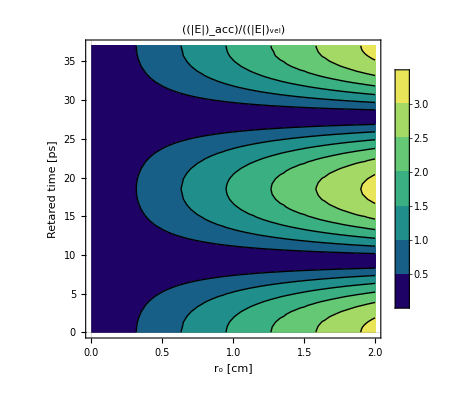

```mathematica
ContourPlot[Ef[Ro/100,t/10^12],{Ro,0,2},{t,0,2Pi/(169646003293.84882)*10^12},PlotTheme->"Scientific",FrameLabel->{"r_o [cm]","Retared time [ps]"},PlotLabel->HoldForm[Subscript["|E|",acc]/Subscript["|E|",vel]],LabelStyle->18,PlotLegends->Automatic,ColorFunction->"BlueGreenYellow"]
```